```mathematica
δ1[p_]:= 2 (Sqrt[6]/4 + p);
δ2[p_]:= 2  (2 p + Sqrt[2 - 32 p^2 + 64 p^4])/(2-32 p^2);



B1[K0_,K1_,α_,p_]:=3/(4 Pi) E^(14 K0) (2K1 α E^3/3)^(1/α) (δ1[p]^α + 6 δ2[p]^α)^(1/α)/p^3;
B2[K0_,K1_,α_,p_]:=(3 Sqrt[2])/(4 Pi) E^(14 K0) (4K1 α E^(7/2)/7)^(1/α) (δ1[p]^α +6  δ2[p]^α)^(1/α)/(p^3 Sqrt[1-2 p]);
BD[K0_,K1_,α_,p_]:=(1+2 p) Exp[3 K0] (3 α Exp[2] K1 / 2)^(1/α)/(Pi p^2);

TruSur[p_]:=2(1+2p)^2
S1[K0_,K1_,α_,p_]:=3/(4 Pi) E^(14 K0) (14K1 α E^3/3)^(1/α) TruSur[p]/p^3;
S2[K0_,K1_,α_,p_]:=(3 Sqrt[2])/(4 Pi) E^(14 K0) (4K1 α E^(7/2))^(1/α) TruSur[p]/(p^3 Sqrt[1-2 p]);

Vol[p_]:= 1/6 (1+2p)^3;
V1[K0_,K1_,α_,p_]:=3/(4 Pi) E^(14 K0) (14K1 α E^3/3)^(1/α) Vol[p]/p^3;
V2[K0_,K1_,α_,p_]:=(3 Sqrt[2])/(4 Pi) E^(14 K0) (4K1 α E^(7/2))^(1/α) Vol[p]/(p^3 Sqrt[1-2 p]);
```

```mathematica
TableForm[Table[{a,Table[{k,FindMinimum[{B1[0,k,a,p],0.1≤ p ≤ 1/4},p][[1]],FindMinimum[{S1[0,k,a,p],0.1≤ p ≤ 1/4},p][[1]],FindMinimum[{V1[0,k,a,p],0.1≤ p ≤ 1/4},p][[1]]},{k,{0.5,1,2}}]},{a,{1,2,3,4,5}}]]
```

1 | 0.5 | 4668.89 | 3222.29 | 402.786
1 | 9337.79 | 6444.57 | 805.572
2 | 18675.6 | 12889.1 | 1611.14
2 | 0.5 | 986.576 | 665.655 | 83.2068
1 | 1395.23 | 941.378 | 117.672
2 | 1973.15 | 1331.31 | 166.414
3 | 0.5 | 537.629 | 357.518 | 44.6897
1 | 677.371 | 450.444 | 56.3055
2 | 853.433 | 567.524 | 70.9405
4 | 0.5 | 386.292 | 254.41 | 31.8012
1 | 459.381 | 302.546 | 37.8183
2 | 546.299 | 359.79 | 44.9737
5 | 0.5 | 313.003 | 204.772 | 25.5965
1 | 359.546 | 235.221 | 29.4026
2 | 413.01 | 270.198 | 33.7747

```mathematica
TableForm[Table[{a,Table[{k,FindMinimum[{B2[0,k,a,p],0.1≤ p ≤ 1/4},p][[1]],FindMinimum[{S2[0,k,a,p],0.1≤ p ≤ 1/4},p][[1]],FindMinimum[{V2[0,k,a,p],0.1≤ p ≤ 1/4},p][[1]]},{k,{0.5,1,2}}]},{a,{1,2,3,4,5}}]]
```

1 | 0.5 | 12061.9 | 9107.4 | 1138.43
1 | 24123.8 | 18214.8 | 2276.85
2 | 48247.7 | 36429.6 | 4553.7
2 | 0.5 | 2139.81 | 1582.63 | 197.829
1 | 3026.15 | 2238.18 | 279.772
2 | 4279.62 | 3165.26 | 395.657
3 | 0.5 | 1099.74 | 802.407 | 100.301
1 | 1385.59 | 1010.97 | 126.371
2 | 1745.73 | 1273.74 | 159.218
4 | 0.5 | 767.391 | 554.771 | 69.3464
1 | 912.587 | 659.738 | 82.4673
2 | 1085.25 | 784.565 | 98.0706
5 | 0.5 | 611.016 | 438.874 | 54.8593
1 | 701.873 | 504.134 | 63.0168
2 | 806.24 | 579.098 | 72.3872

```mathematica
FindMinimum[{B2[0,1,1,p],0.1≤ p ≤ 1/4},p][[1]]
```

24123.8

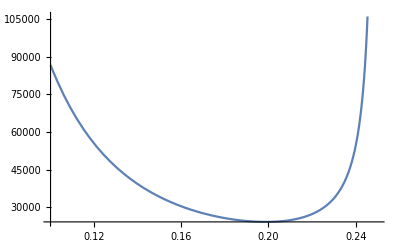

```mathematica
Plot[B2[0,1,1,p],{p,0.1,1/4}]
```

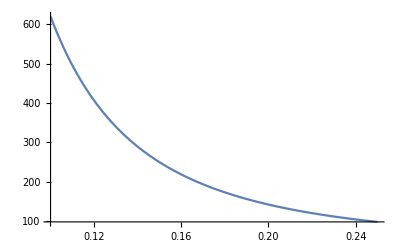

```mathematica
Plot[V2[0,2,4,p],{p,0.1,1/4}]
```

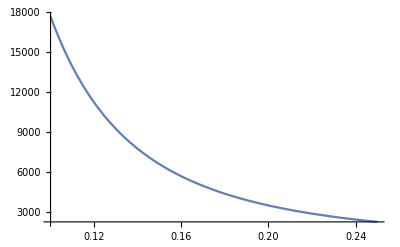

```mathematica
Plot[S2[0,1,2,p],{p,0.1,1/4}]
```